```mathematica
SetDirectory[NotebookDirectory[]];
```

### Compare no corr and corr w=10000

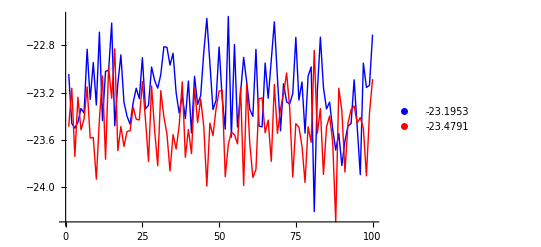

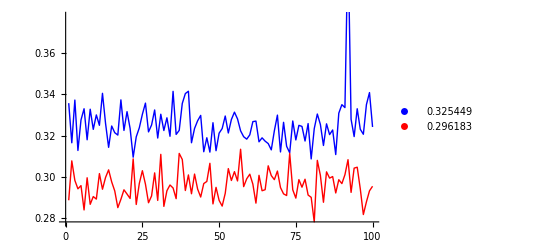

```mathematica
mmin=1;
corrdata=Import["he4ip.vmc.10000.dat"];
nocorrdata=Import["he4noip.vmc.10000.dat"];
corrE=Transpose[corrdata][[4]];
nocorrE=Transpose[nocorrdata][[4]];
corrσ=Transpose[corrdata][[6]];
nocorrσ=Transpose[nocorrdata][[6]];

ipmean=Mean[corrE[[mmin;;Length[corrdata]]]];
nomean=Mean[nocorrE[[mmin;;Length[nocorrdata]]]];
iperr=Sqrt[Total[corrσ^2]/Length[corrσ]];
noerr=Sqrt[Total[nocorrσ^2]/Length[nocorrσ]];

ListPlot[{nocorrE,corrE},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{nomean,ipmean}]
ListPlot[{nocorrσ,corrσ},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{noerr,iperr}]
```

DATA BEFORE OPTIMIZATION (WITH 24000 WALKERS NOT 10000):
No ip corelations: E=-23.3(2)
With ip correlations: E=-23.7(2)

### Compare no corr and corr w=10000

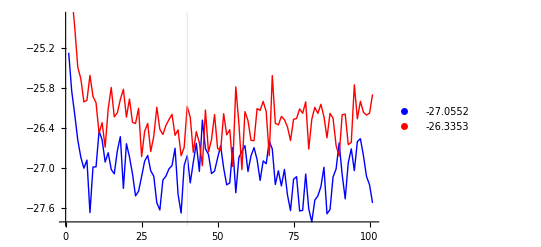

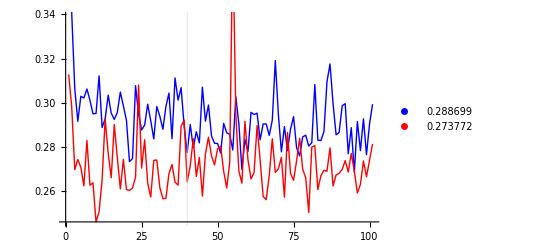

```mathematica
mmin=40;
corrdata=Import["he4ip.dmc.10000.dat"];
nocorrdata=Import["he4noip.dmc.10000.dat"];
corrE=Transpose[corrdata][[4]];
nocorrE=Transpose[nocorrdata][[4]];
corrσ=Transpose[corrdata][[6]];
nocorrσ=Transpose[nocorrdata][[6]];

corrl=Length[corrE];
nocorrl=Length[nocorrE];
ipmean=Mean[corrE[[mmin;;corrl]]];
nomean=Mean[nocorrE[[mmin;;nocorrl]]];
iperr=Sqrt[Total[corrσ[[mmin;;corrl]]^2]/Length[corrσ[[mmin;;corrl]]]];
noerr=Sqrt[Total[nocorrσ[[mmin;;nocorrl]]^2]/Length[nocorrσ[[mmin;;nocorrl]]]];

ListPlot[{nocorrE,corrE},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{nomean,ipmean},GridLines->{{mmin},{}},GridLinesStyle->Directive[Thick]]
ListPlot[{nocorrσ,corrσ},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{noerr,iperr},GridLines->{{mmin},{}},GridLinesStyle->Directive[Thick]]
```

DATA BEFORE OPTIMIZATION:
No ip corelations: E=-27.1(3)
With ip correlations: E=-26.4(3)

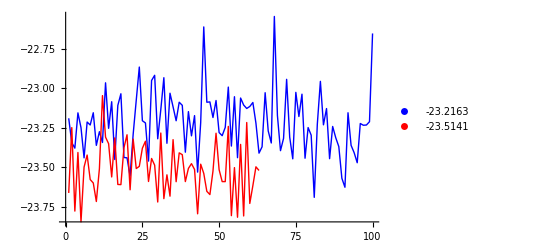

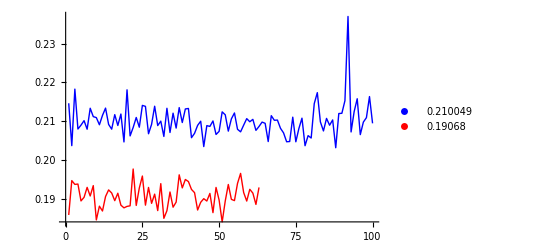

```mathematica
mmin=1;
corrdata=Import["he4ip.vmc.24000.dat"];
nocorrdata=Import["he4noip.vmc.24000.dat"];
corrE=Transpose[corrdata][[4]];
nocorrE=Transpose[nocorrdata][[4]];
corrσ=Transpose[corrdata][[6]];
nocorrσ=Transpose[nocorrdata][[6]];

ipmean=Mean[corrE[[mmin;;Length[corrdata]]]];
nomean=Mean[nocorrE[[mmin;;Length[nocorrdata]]]];
iperr=Sqrt[Total[corrσ^2]/Length[corrσ]];
noerr=Sqrt[Total[nocorrσ^2]/Length[nocorrσ]];

ListPlot[{nocorrE,corrE},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{nomean,ipmean}]
ListPlot[{nocorrσ,corrσ},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{noerr,iperr}]
```

### Compare noip pion with stampede w=10000

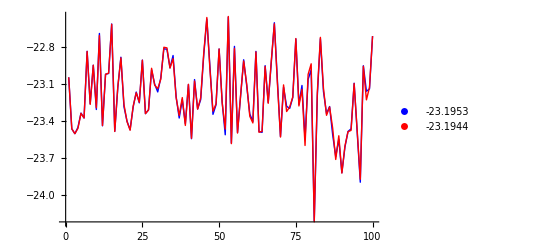

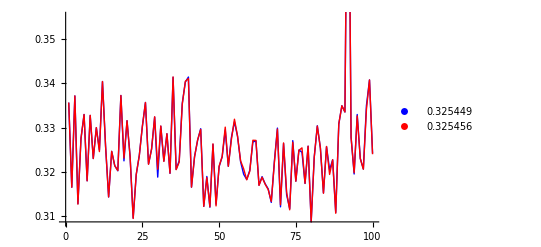

```mathematica
mmin=1;
corrdata=Import["dat.6602806"];
nocorrdata=Import["he4noip.vmc.10000.dat"];
corrE=Transpose[corrdata][[4]];
nocorrE=Transpose[nocorrdata][[4]];
corrσ=Transpose[corrdata][[6]];
nocorrσ=Transpose[nocorrdata][[6]];

ipmean=Mean[corrE[[mmin;;Length[corrdata]]]];
nomean=Mean[nocorrE[[mmin;;Length[nocorrdata]]]];
iperr=Sqrt[Total[corrσ^2]/Length[corrσ]];
noerr=Sqrt[Total[nocorrσ^2]/Length[nocorrσ]];

ListPlot[{nocorrE,corrE},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{nomean,ipmean}]
ListPlot[{nocorrσ,corrσ},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{noerr,iperr}]
```

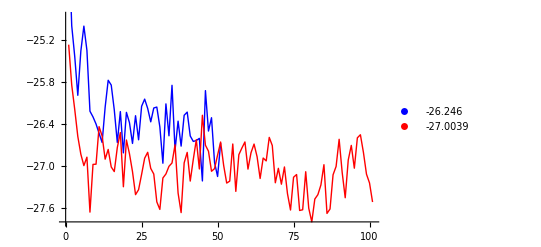

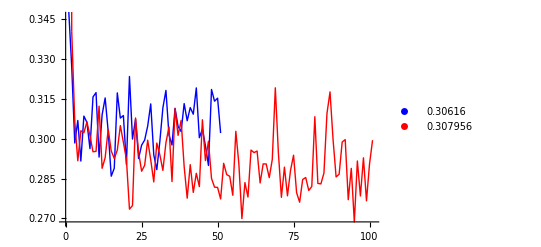

```mathematica
mmin=1;
corrdata=Import["he4noip.dmc.10000.dat"];
nocorrdata=Import["dat.6884809"];
corrE=Transpose[corrdata][[4]];
nocorrE=Transpose[nocorrdata][[4]];
corrσ=Transpose[corrdata][[6]];
nocorrσ=Transpose[nocorrdata][[6]];

ipmean=Mean[corrE[[mmin;;Length[corrdata]]]];
nomean=Mean[nocorrE[[mmin;;Length[nocorrdata]]]];
iperr=Sqrt[Total[corrσ^2]/Length[corrσ]];
noerr=Sqrt[Total[nocorrσ^2]/Length[nocorrσ]];

ListPlot[{nocorrE,corrE},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{nomean,ipmean}]
ListPlot[{nocorrσ,corrσ},Joined->True,PlotStyle->{{Blue},{Red}},PlotLegends->{noerr,iperr}]
```

### Get error

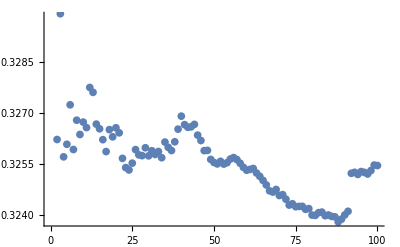

```mathematica
data=Import["he4ip.vmc.10000.dat"];
data=Import["he4noip.vmc.10000.dat"];
max=100;
error=Transpose[data][[6]][[1;;max]];

cumerr[indata_,n_]:=Module[{temp,aveerr},
temp=indata[[1;;n]];
aveerr=√(Total[temp^2]/n);
aveerr
]

plotdata=Range[1,max]*0;
For[i=1,i≤Length[error],i++,
plotdata[[i]]={i,cumerr[error,i]};
]

ListPlot[plotdata]
```